```mathematica
En[L_,a_] := (3L+12L^5+2a/Sqrt[π])/(8L^3);
```

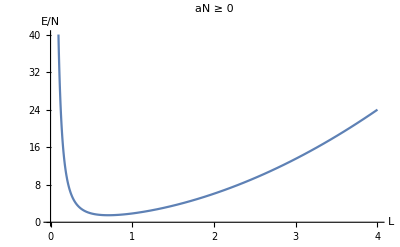

```mathematica
Plot[En[L,0],{L,0,4},AxesLabel->{L,"E/N"},PlotLabel->"aN ≥ 0"]
```

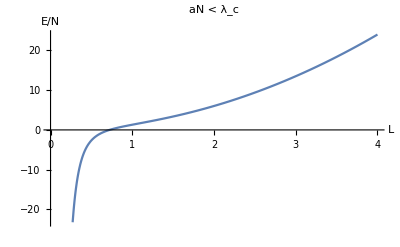

```mathematica
Plot[En[L,-4],{L,0,4},AxesLabel->{L,"E/N"},PlotLabel->"aN < λ_c"]
```

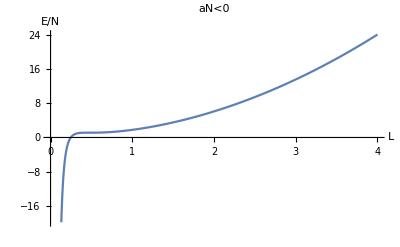

```mathematica
Plot[En[L,-(2 √(2 π))/(5 5^(1/4))],{L,0,4},AxesLabel->{L,"E/N"},PlotLabel->"aN<0"]
```

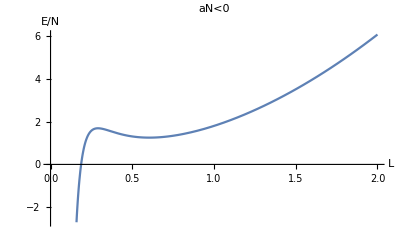

```mathematica
Plot[En[L,-.5],{L,0,2},AxesLabel->{L,"E/N"},PlotLabel->"aN<0"]
```

```mathematica
Solve[{D[En[L,a],{L,2}]==0,D[En[L,a],{L,1}]==0},]
```

{}

```mathematica
D[En[L,a],{L,2}]
```

30-(3 (3+60 L^4))/(4 L^4)+(3 (3 L+12 L^5+(2 a)/(√π)))/(2 L^5)

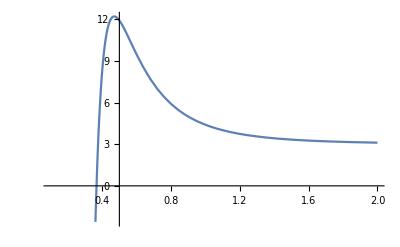

```mathematica
Plot[30-(3 (3+60 L^4))/(4 L^4)+(3 (3 L+12 L^5+-1/(√π)))/(2 L^5),{L,0.1,2}]
```

```mathematica
Solve[{D[En[L,a],{L,2}]==0,D[En[L,a],{L,1}]==0},{a,L}]
```

{{a→(2 √(2 π))/(5 5^(1/4)),L→-1/(√2 5^(1/4))},{a→(2 ⅈ √(2 π))/(5 5^(1/4)),L→-ⅈ/(√2 5^(1/4))},{a→-(2 ⅈ √(2 π))/(5 5^(1/4)),L→ⅈ/(√2 5^(1/4))},{a→-(2 √(2 π))/(5 5^(1/4)),L→1/(√2 5^(1/4))}}

```mathematica
D[En[L,a],{L,2}]//FullSimplify
```

3+9/(4 L^4)+(3 a)/(L^5 √π)